Mohamed M. Hammad

Neural Network and Deep Learning with Mathematica                              < >    Ξ

Edited by Hao Feng

## 8 Regularization Techniques

Remark:
This chapter provides a Mathematica implementation of the concepts and ideas presented in Chapter 7, [1], of the book titled Artificial Neural Network and Deep Learning: Fundamentals and Theory. We strongly recommend that you begin with the theoretical chapter to build a solid foundation before exploring the corresponding practical implementation.

In machine learning, particularly in the field of deep learning, the complexity of models often leads to a significant challenge: overfitting. Overfitting occurs when a model learns the detail and noise in the training data to an extent that it negatively impacts the performance of the model on new data. The essence of regularization is to constrain our model in such a way that it avoids overfitting and thus performs better on unseen datasets. This chapter offers a comprehensive exploration of the strategies used to improve the generalization ability of neural networks (NNs). By introducing regularization techniques into the training process, we aim to develop models that are not only accurate on the training data but also robust and adaptable to new, unseen data. This chapter will cover three principal regularization techniques: penalty-based regularization, early stopping, and ensemble methods (dropout), each addressing overfitting in a unique way.

Penalty-Based Regularization:

Penalty-Based Regularization involves modifying the loss function by adding a penalty term to it. This term penalizes certain values of model parameters to discourage complexity:

• 𝐿_1 regularization (Lasso) promotes sparsity by adding a penalty equivalent to the absolute value of the coefficients, which can reduce the number of features in the model [127-138].

• 𝐿_2 regularization (Ridge) adds a penalty equivalent to the square of the magnitude of the coefficients, encouraging the model parameters to be small and distributing the error among them.

• Elastic net combines both 𝐿_1 and 𝐿_2 penalties and is useful when there are correlations among features.

Early Stopping:

Early Stopping is a different kind of regularization technique that does not modify the loss function but rather alters the training process itself. Early stopping involves monitoring the model’s performance on a validation set and stopping the training as soon as the performance starts to degrade, despite improvements on the training set. This method not only helps in preventing overfitting but also saves computational resources by reducing unnecessary training iterations.

Ensemble Methods (Dropout):

Ensemble methods [139,140], with focus on dropout, is a powerful regularization technique particularly popular in training deep NNs. Unlike penalty-based methods, dropout works by randomly deactivating a subset of neurons in each training iteration. This randomness helps to break up situations where network layers co-adapt to correct mistakes from prior layers, thus making the model more capable of generalizing well.

By integrating these regularization techniques, machine learning practitioners can enhance model performance significantly. This chapter will equip you with the knowledge to understand these methods conceptually, ensuring that your NNs are not just powerful, but also robust and efficient.

This chapter delves into three essential regularization techniques implemented in Mathematica: L2Regularization, TrainingStoppingCriterion, and DropoutLayer. Each method addresses overfitting from a unique perspective, offering a robust toolkit for building and fine-tuning machine learning models.

In Mathematica, 𝐿_2-regularization can be applied by specifying the L2Regularization suboption within the Method option of the NetTrain function. This integration allows users to seamlessly incorporate 𝐿_2 regularization into the training process, enhancing the model’s ability to generalize.

An effective way to prevent overfitting is to stop the training process at the right moment before the model begins to overfit the training data. The TrainingStoppingCriterion option in NetTrain provides a systematic approach to determine when to halt training. This criterion can be based on various metrics, such as validation loss or accuracy, ensuring that the training process concludes when the model reaches optimal performance on validation data. Implementing a training stopping criterion helps in maintaining the model’s generalization capability by avoiding excessive training.

In Mathematica, the DropoutLayer can be integrated into NN architectures, providing an easy-to-use mechanism for applying dropout regularization.

### 𝑳_2 Regularization

In Mathematica, during the training of neural networks with the NetTrain function, you can apply ℓ2 regularization by specifying L2Regularization as a suboption of the Method option. This regularization helps prevent overfitting by penalizing larger weights in the model’s loss function.

The suboption “L2Regularization” can be given in the following forms:

r				use the value r for all weights in the net

{lspec1->r1,lspec2->r2,…}	use the value ri for the specific part lspeci of the net

code 8.1

(* The code aims to demonstrate the process of training neural networks on synthetic data, evaluating overfitting, and applying regularization to improve model performance. It generates synthetic data with Gaussian noise, visualizes this data, and constructs a neural network with two hidden layers. The network is trained on the data, and its predictions are compared to the original data to assess overfitting. A test dataset is generated to evaluate the network’s performance using a mean squared loss function. The neural network is then retrained with L2 regularization to prevent overfitting, and the performance of the regularized model is compared to the overfitted model to highlight the benefits of regularization: *)

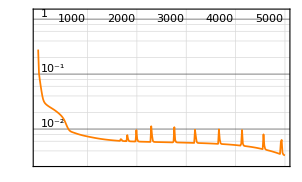
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:5000  rounds:5000  time:12s  examples/s:12926
data | ,,  training examples:31  processed examples:155000  skipped examples:0
method | ,,  ADAMoptimizer  batch size31CPU
round | ,,  loss:3.32×10^-3
 | rounds
loss | -Graphics- | 
 | ]

The average loss of most recent round is: 0.00331655

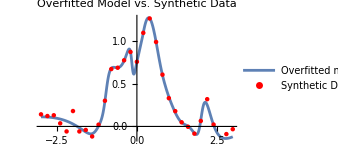

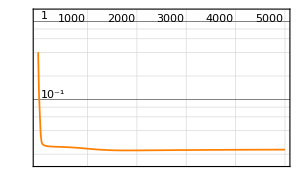
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:5000  rounds:5000  time:17s  examples/s:9569
data | ,,  training examples:31  processed examples:155000  skipped examples:0
method | ,,  SGDoptimizer  batch size31CPU
round | ,,  loss:2.28×10^-2
 | rounds
loss | -Graphics- | 
 | ]

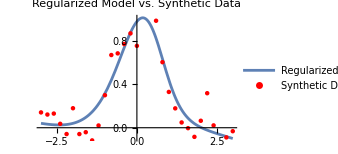

The mean test loss for the L2 regularized network is: 0.0276673

The mean test loss for the overfitted network is: 0.0386161

```mathematica
syntheticData=Table[
x->Exp[-x^2]+RandomVariate[NormalDistribution[0,0.15]],
{x,-3,3,0.2}
];

dataPlot=ListPlot[
List@@@syntheticData,
PlotStyle->Red,
ImageSize->250,
PlotLegends->{"Synthetic Data"},
AxesLabel->{"x","y"},
PlotLabel->"Synthetic Data with Gaussian Noise"
];

neuralNetwork=NetChain[
{
150,Tanh,
150,Tanh,
1
}
];

trainingResults=NetTrain[
neuralNetwork,
syntheticData,
All,
MaxTrainingRounds->5000
]

Print["The average loss of most recent round is: ", trainingResults["RoundLoss"]];

overfittedNetwork=trainingResults["TrainedNet"];

overfitPlot=Show[
Plot[
overfittedNetwork[x],
{x,-3,3},
PlotLegends->{"Overfitted model"}
],
dataPlot,
PlotLabel->"Overfitted Model vs. Synthetic Data",
ImageSize->250
]

testData=Table[
x->Exp[-x^2]+RandomVariate[NormalDistribution[0,0.15]],
{x,-3,3,0.2}
];
testXValues=Keys[testData];
testYValues=Values[testData];

calculateMeanTestLoss[network_]:=SquaredEuclideanDistance[network[testXValues],testYValues]/Length[testXValues];
regularizedTrainingResults=NetTrain[
neuralNetwork,
syntheticData,
All,
Method->{"SGD","L2Regularization"->0.01},
MaxTrainingRounds->5000
]
regularizedNetwork=regularizedTrainingResults["TrainedNet"];
regularizedPlot=Show[
Plot[
regularizedNetwork[x],
{x,-3,3},
PlotLegends->{"Regularized Model"}
],
dataPlot,
PlotLabel->"Regularized Model vs. Synthetic Data",
ImageSize->250
]

Print[
"The mean test loss for the L2 regularized network is: ",
calculateMeanTestLoss[regularizedNetwork]
];

Print[
"The mean test loss for the overfitted network is: ",
calculateMeanTestLoss[overfittedNetwork]
];
```

code 8.2

(* The code demonstrates the impact of different L2 regularization rates on neural network performance when fitting noisy synthetic data. It defines a function g(x)=exp(−x^2) and generates synthetic data by adding Gaussian noise to this function. The code specifies three L2 regularization rates, constructs neural networks with the same architecture for each rate, and trains these networks on the synthetic data using stochastic gradient descent. The trained networks’ predictions are plotted alongside the original data to visually compare the effects of the different regularization rates, highlighting how L2 regularization helps mitigate overfitting: *)

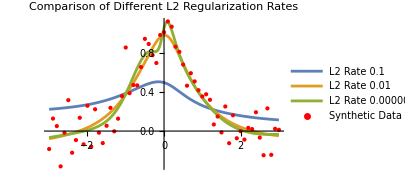

```mathematica
g[x_]:=Exp[-x^2];
syntheticData=Table[x->g[x]+RandomVariate[NormalDistribution[0,0.15]],{x,-3,3,0.1}];

regularizationRates={0.1,0.01,0.000001};

neuralNetworks=Table[
NetChain[
{
100,Tanh,
100,Tanh,
1
}
],
{rate,regularizationRates}
];

trainedNetworks=Table[
NetTrain[
neuralNetworks[[i]],
syntheticData,
MaxTrainingRounds->5000,
Method->{"SGD","L2Regularization"->regularizationRates[[i]]}
],
{i,1,Length[regularizationRates]}
];

Show[
Plot[
{trainedNetworks[[1]][x],trainedNetworks[[2]][x],trainedNetworks[[3]][x]},
{x,-3,3},
ImageSize->300,
PlotRange->All,
PlotLegends->{"L2 Rate 0.1","L2 Rate 0.01","L2 Rate 0.000001"},
PlotLabel->"Comparison of Different L2 Regularization Rates"
],
ListPlot[
List@@@syntheticData,
PlotStyle->{Red,PointSize[0.01]},
PlotLegends->{"Synthetic Data"}
]
]
```

### TrainingStoppingCriterion

TrainingStoppingCriterion is an option for NetTrain that specifies a criterion for stopping training early in order to prevent overfitting.

Setting TrainingStoppingCriterion->”measurement” specifies that training should be stopped if measurement stops improving. Possible values for measurement include:

“Loss”		network training loss

key		a TrainingProgressMeasurements key

Remarks:

• TrainingStoppingCriterion->Automatic is equivalent to TrainingStoppingCriterion->”Loss”.

• If the validation set is present, the stopping criterion is checked whenever the validation loss and metrics are calculated (once per round by default); otherwise, the stopping criterion is checked once per round.

• TrainingStoppingCriterion has a number of suboptions that can be specified using the <|”Criterion”- >”measurement”,opt1->val1,opt2->val2,…|> syntax.

• Setting TrainingStoppingCriterion-> <|”Criterion”->”measurement”,”Patience”->n|> specifies that training should be stopped if an improvement in measurement is not seen for n rounds in a row. The default value for n is 0.

• Setting TrainingStoppingCriterion-> <|”Criterion”->”measurement”,”InitialPatience”->n |> specifies that the stopping criterion is only checked for the first time after n rounds. The default value for n is 0.

• Setting TrainingStoppingCriterion-> <|”Criterion”->”measurement”, “Improvement”->v|> specifies the minimum change in measurement that is considered an improvement. Possible values for improvement are:

“AbsoluteChange”	stop training if measurement improves by less than v

“RelativeChange”	stop training if measurement improves by less than a factor v of the current best value

• If an improvement specification is not given, then “AbsoluteChange”->0 is used.

• It is also possible to specify a function as the stopping criterion using TrainingStoppingCriterion-> <|”Criterion”->func,…|>, where func should return True if training should be stopped.

code 8.3

(* The code trains a neural network on synthetic data generated from a Gaussian- like function with noise, using various training strategies and early stopping criteria to explore their effects on model performance and overfitting. The code first trains a network without stopping criteria to potentially overfit the data, then applies different forms of early stopping based on validation loss improvements (absolute, relative, and after a set number of rounds) to prevent overfitting and enhance generalization. Each model’s performance is visualized against the training data, providing a clear comparison of how each stopping criterion influences the learning process and the model’s ability to generalize beyond the training set: *)

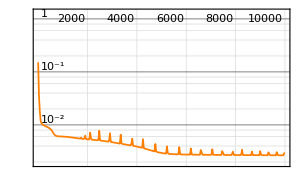
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:10000  rounds:10000  time:33s  examples/s:9427
data | ,,  training examples:31  processed examples:310000  skipped examples:0
method | ,,  ADAMoptimizer  batch size31CPU
round | ,,  loss:2.81×10^-3
 | rounds
loss | -Graphics- | 
 | ]

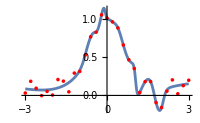

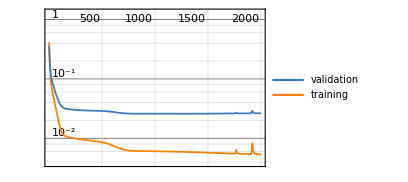
| rounds
loss | -Graphics-

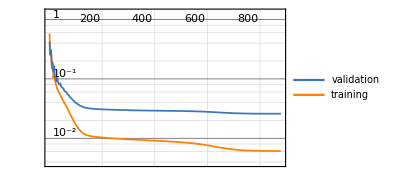
| rounds
loss | -Graphics-

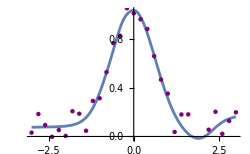

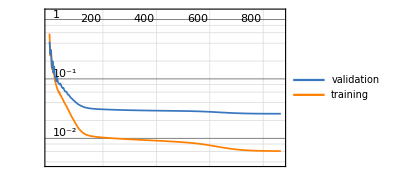
| rounds
loss | -Graphics-

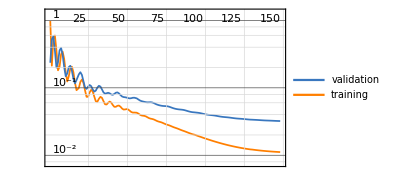
| rounds
loss | -Graphics-

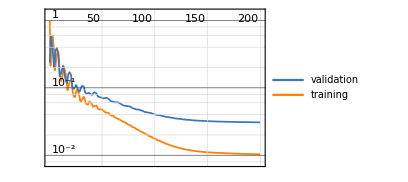
| rounds
loss | -Graphics-

```mathematica
dataFunction[x_]:=Exp[-x^2];
noiseLevel=0.15;

trainingData=Table[
x->dataFunction[x]+RandomVariate[NormalDistribution[0,noiseLevel]],
{x,-3,3,0.2}
];

validationData=Table[
x->dataFunction[x]+RandomVariate[NormalDistribution[0,noiseLevel]],
{x,-3,3,0.1}
];

initialNetwork=NetChain[
{
150,Tanh,
150,Tanh,
1
}
];
initialTrainingResults=NetTrain[
initialNetwork,
trainingData,
All,
MaxTrainingRounds->10000
]

overfittedNetwork=initialTrainingResults["TrainedNet"];

Show[
Plot[
overfittedNetwork[x],
{x,-3,3},
ImageSize->200
],
ListPlot[
List@@@trainingData,
PlotStyle->Red
]
]

basicTrainingResults=NetTrain[
initialNetwork,
trainingData,
"LossPlot",
ValidationSet->validationData,
MaxTrainingRounds->2000
]

earlyStoppingResults=NetTrain[
initialNetwork,
trainingData,
All,
ValidationSet->validationData,
MaxTrainingRounds->2000,
TrainingStoppingCriterion-><|"Criterion"->"Loss","Patience"->10|>
];

earlyStoppedNetwork=earlyStoppingResults["TrainedNet"];
earlyStoppingResults["LossPlot"]

Show[
Plot[
earlyStoppedNetwork[x],
{x,-3,3},
ImageSize->250
],
ListPlot[
List@@@trainingData,
PlotStyle->Purple
]
]

delayedStoppingResults=NetTrain[
initialNetwork,
trainingData,
"LossPlot",
ValidationSet->validationData,
TrainingStoppingCriterion-><|"Criterion"->"Loss","InitialPatience"->300|>
]

fineGrainedStoppingResultsAbsolute=NetTrain[
initialNetwork,
trainingData,
"LossPlot",
ValidationSet->validationData,
TrainingStoppingCriterion-><|"Criterion"->"Loss","AbsoluteChange"->0.0001,"Patience"->10|>
]

fineGrainedStoppingResultsRelative=NetTrain[
initialNetwork,
trainingData,
"LossPlot",
ValidationSet->validationData,
TrainingStoppingCriterion-><|"Criterion"->"Loss","RelativeChange"->0.01,"InitialPatience"->200|>
]
```

code 8.4

(* The code is designed to create, train, and evaluate a neural network for binary classification. It begins by generating synthetic training and validation datasets consisting of points within a unit disk, labeled based on their proximity to the origin. The network, composed of two linear layers with Tanh and Logistic Sigmoid activations, is trained using metrics like recall and accuracy, and employs an early stopping criterion based on recall to prevent overfitting. Post-training, the code visualizes the decision boundary, displays training performance plots, and extracts the trained network for further analysis, effectively demonstrating an end-to-end machine learning pipeline within a binary classification context: *)

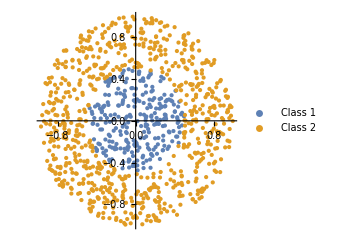

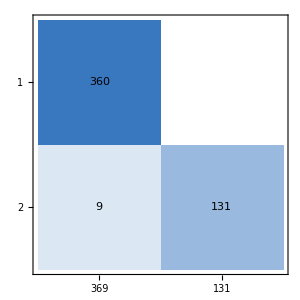
<|Loss→0.130755,Recall→0.935714,Accuracy→0.982,ConfusionMatrixPlot→actual class | -Graphics-
 | predicted class|>

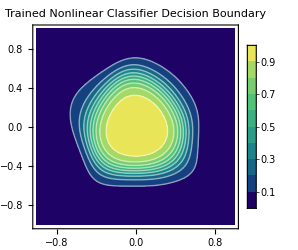

KeyAbsent

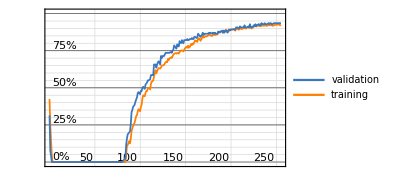
| rounds
recall | -Graphics-

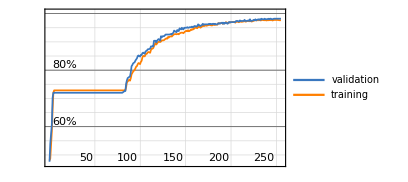
| rounds
accuracy | -Graphics-

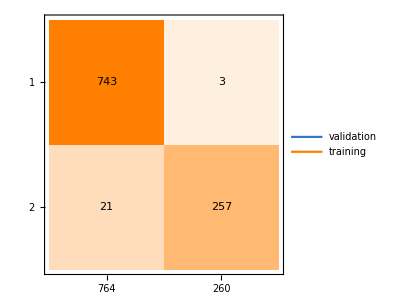
actual class | -Graphics-
 | predicted class
actual class | -Graphics-
 | predicted class

```mathematica
trainpoints=RandomPoint[Disk[],1000];
trainlabels=Thread[Map[Norm,trainpoints]<0.5];
trainingData=trainpoints->trainlabels;

validationPoints=RandomPoint[Disk[],500];
validationLabels=Thread[Map[Norm,validationPoints]<0.5];
validationData=validationPoints->validationLabels;

ListPlot[
{
Pick[trainpoints,trainlabels,True],
Pick[trainpoints,trainlabels,False]
},
AspectRatio->1,
ImageSize->250,
PlotStyle->PointSize[Medium],
FrameLabel->{"X","Y","Synthetic Training Set"},
PlotLegends->{"Class 1","Class 2"}
]

net=NetChain[
{
LinearLayer[20],ElementwiseLayer[Tanh],
LinearLayer[],ElementwiseLayer[LogisticSigmoid]},
"Output"->NetDecoder["Boolean"]
];

netTrainResults=NetTrain[
net,
trainingData,
All,
ValidationSet->validationData,
TrainingProgressMeasurements->{"Recall","Accuracy","ConfusionMatrixPlot"},
TrainingStoppingCriterion-><|"Criterion"->"Recall","InitialPatience"->150,"Patience"->20|>
];

netTrainResults["ValidationMeasurements"]
trainedNet=netTrainResults["TrainedNet"];

ContourPlot[
trainedNet[{x,y},None],
{x,-1,1},
{y,-1,1},
ContourStyle->{White},
ClippingStyle->Automatic,
ColorFunction->"BlueGreenYellow",
PlotLegends->Automatic,
LabelStyle->Directive[Black,10],
ImageSize->250,
PlotLabel->"Trained Nonlinear Classifier Decision Boundary"]

lossPlot=netTrainResults["FInalPlots"][[1]]
recallPlot=netTrainResults["FinalPlots"][[2]]
accuracyPlot=netTrainResults["FinalPlots"][[3]]
confusionmatrixPlot=netTrainResults["FinalPlots"][[4]]
```

code 8.5

(* The previous code uses early stopping based on the recall metric, ceasing training if recall fails to improve within defined patience parameters. In contrast, the following code stops training based on validation loss, halting the process if the loss remains below a threshold of 0.3 for more than 10 consecutive validation checks. These differences highlight alternative approaches to preventing overfitting, with the first method prioritizing a specific performance metric (recall), and the second emphasizing overall error minimization: *)

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1872  rounds:117  time:8.1s  examples/s:14789
data | ,,  training examples:1000  validation examples:500  processed examples:119808  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:2.72×10^-1  recall:67.2%  acc.:91.89%
validation | ,,  loss:2.66×10^-1  recall:73.4%  acc.:93.20%
 | 
-Graphics-  training set	-Graphics-  validation set | ]

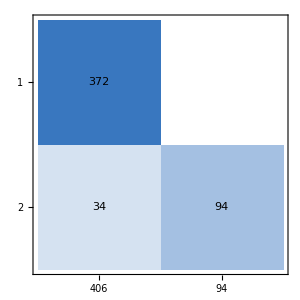
<|Loss→0.266039,Recall→0.734375,Accuracy→0.932,ConfusionMatrixPlot→actual class | -Graphics-
 | predicted class|>

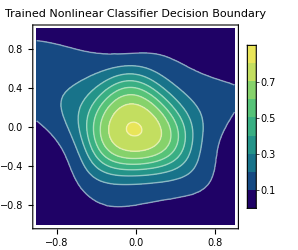

```mathematica
trainpoints=RandomPoint[Disk[],1000];
trainlabels=Thread[Map[Norm,trainpoints]<0.5];
trainingData=trainpoints->trainlabels;

validationPoints=RandomPoint[Disk[],500];
validationLabels=Thread[Map[Norm,validationPoints]<0.5];
validationData=validationPoints->validationLabels;

net=NetChain[
{
20,Tanh,
LinearLayer[],LogisticSigmoid},
"Output"->NetDecoder["Boolean"]
];

netTrainResults=NetTrain[
net,
trainingData,
All,
ValidationSet->validationData,
TrainingProgressMeasurements->{"Recall","Accuracy","ConfusionMatrixPlot"},
TrainingStoppingCriterion-><|"Criterion"->Function[#ValidationLoss<0.3],"Patience"->10|>
]

netTrainResults["ValidationMeasurements"]
trainedNet=netTrainResults["TrainedNet"];

ContourPlot[
trainedNet[{x,y},None],
{x,-1,1},
{y,-1,1},
ContourStyle->{White},
ClippingStyle->Automatic,
ColorFunction->"BlueGreenYellow",
PlotLegends->Automatic,
LabelStyle->Directive[Black,10],
ImageSize->250,
PlotLabel->"Trained Nonlinear Classifier Decision Boundary"
]
```

code 8.6

(* The direction of change that is considered an improvement depends on the measurement. For “Loss”, a decrease is an improvement. For other measurements, the direction can be specified using the “Direction”->direction suboption of TrainingProgressMeasurements. For built-in measurements, the direction is automatically chosen as appropriate: *)

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:384  rounds:24  time:0.58s  examples/s:42450
data | ,,  training examples:1000  validation examples:500  processed examples:24576  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:5.54×10^-1  1/Output:7.89
validation | ,,  loss:5.38×10^-1  1/Output:8.06
 | 
-Graphics-  training set	-Graphics-  validation set | ]

<|Loss→0.538018,1/Output→8.06298|>

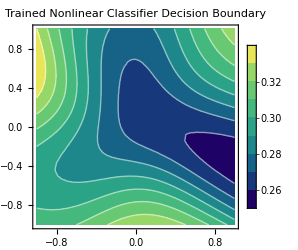

```mathematica
trainpoints=RandomPoint[Disk[],1000];
trainlabels=Thread[Map[Norm,trainpoints]<0.5];
trainingData=trainpoints->trainlabels; 
validationPoints=RandomPoint[Disk[],500]; validationLabels=Thread[Map[Norm,validationPoints]<0.5];
validationData=validationPoints->validationLabels;

net=NetChain[
{
20,Tanh,
LinearLayer[],LogisticSigmoid},
"Output"->NetDecoder["Boolean"]
];

netTrainResults=NetTrain[
net,
trainingData,
All,
ValidationSet->validationData,
TrainingProgressMeasurements-><|"Measurement"->NetPort[{"1","Output"}],"Aggregation"->"L1Norm","Direction"->"Increasing"
|>,
TrainingStoppingCriterion-><|"Criterion"->"1/Output","Patience"->9
|>
]

netTrainResults["ValidationMeasurements"]
trainedNet=netTrainResults["TrainedNet"];

ContourPlot[trainedNet[{x,y},None],{x,-1,1},{y,-1,1},

ContourStyle->{White},ClippingStyle->Automatic,ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,LabelStyle->Directive[Black,10],ImageSize->250,PlotLabel->"Trained Nonlinear Classifier Decision Boundary"]
```

### DropoutLayer

DropoutLayer[] represents a net layer that sets its input elements to zero with probability 0.5 during training.

DropoutLayer[p] sets its input elements to zero with probability p during training.

Possible explicit settings for the Method option include:

“AlphaDropout”	keeps the mean and variance of the input constant; designed to be used together with the ElementwiseLayer[“SELU”] activation

“Dropout”		sets the input elements to zero with probability p during training, multiplying the remainder by 1/(1-p)

Remarks:

• DropoutLayer normally infers the dimensions of its input from its context in NetChain etc. To specify the dimensions explicitly as {n1,n2,…}, use DropoutLayer[“Input”->{n1,n2,…}].

• DropoutLayer[…][input] explicitly computes the output from applying the layer.

• DropoutLayer[…][{input1,input2,…}] explicitly computes outputs for each of the inputi.

• DropoutLayer only randomly sets input elements to zero during training. During evaluation, DropoutLayer leaves the input unchanged, unless NetEvaluationMode->”Train” is specified when applying the layer.

code 8.7

```mathematica
drop=DropoutLayer[]
drop[{1,2,3,4,5}]
drop[{1,2,3,4,5},NetEvaluationMode->"Train"]
```

DropoutLayer[…]

{1.,2.,3.,4.,5.}

{2.,4.,0.,8.,0.}

code 8.8

```mathematica
drop=DropoutLayer[0.8]
drop[{1,2,3,4,5,6,7,8,9,10}]
drop[{1,2,3,4,5,6,7,8,9,10},NetEvaluationMode->"Train"]
```

DropoutLayer[…]

{1.,2.,3.,4.,5.,6.,7.,8.,9.,10.}

{5.,0.,15.,0.,25.,0.,0.,40.,0.,50.}

code 8.9

```mathematica
drop=DropoutLayer[Method->"AlphaDropout"]
drop[{1,2,3,4,5,6,7},NetEvaluationMode->"Train"]
```

DropoutLayer[…]

{1.6656,-0.779194,-0.779194,4.32481,5.21122,-0.779194,6.98403}

code 8.10

(* The code demonstrates the process of training neural networks on synthetic data, visualizing the effects of overfitting, and evaluating the effectiveness of dropout as a regularization technique. It generates synthetic data based on the function exp(−x^2) with added Gaussian noise and visualizes this data. A basic neural network is defined and trained on the synthetic data, and its overfitted predictions are plotted. New test data is generated for performance evaluation. Additionally, a dropout neural network is defined and trained to prevent overfitting. The predictions of both the overfitted and dropout networks are visualized, and their performance is compared by calculating and comparing the mean squared error on the test set, highlighting the benefits of dropout in improving generalization: *)

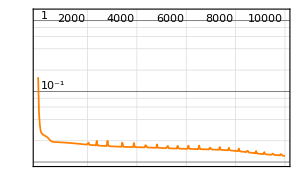
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:10000  rounds:10000  time:20s  examples/s:31567
data | ,,  training examples:61  processed examples:610000  skipped examples:0
method | ,,  ADAMoptimizer  batch size61CPU
round | ,,  loss:1.22×10^-2
 | rounds
loss | -Graphics- | 
 | ]

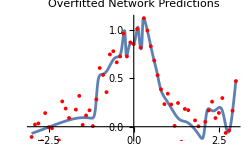

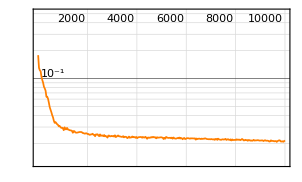
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:10000  rounds:10000  time:19s  examples/s:32246
data | ,,  training examples:61  processed examples:610000  skipped examples:0
method | ,,  ADAMoptimizer  batch size61CPU
round | ,,  loss:2.09×10^-2
 | rounds
loss | -Graphics- | 
 | ]

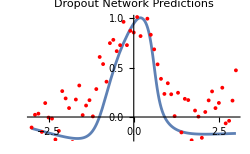

{0.0755019,0.035243}

```mathematica
syntheticData=Table[
x->Exp[-x^2]+RandomVariate[NormalDistribution[0,0.15]],
{x,-3,3,0.1}
];

dataPlot=ListPlot[
List@@@syntheticData,
PlotStyle->Red,
PlotLabel->"Synthetic Data"
];

basicNeuralNetwork=NetChain[
{
150,Tanh,
150,Tanh,
1
}
];

trainingResultsBasic=NetTrain[
basicNeuralNetwork,
syntheticData,
All,
MaxTrainingRounds->10000
]

overfittedNetwork=trainingResultsBasic["TrainedNet"];

Show[
Plot[
overfittedNetwork[x],
{x,-3,3},
ImageSize->250,
PlotLabel->"Overfitted Network Predictions"
],
dataPlot]

testData=Table[
x->Exp[-x^2]+RandomVariate[NormalDistribution[0,0.15]],
{x,-3,3,0.1}
];

testInputs=Keys[testData];
testOutputs=Values[testData];

dropoutNeuralNetwork=NetChain[
{
150,DropoutLayer[0.8],Tanh,
150,Tanh,
1
}
];

trainingResultsDropout=NetTrain[
dropoutNeuralNetwork,
syntheticData,
All,
MaxTrainingRounds->10000
]

trainedDropoutNetwork=trainingResultsDropout["TrainedNet"];

Show[
Plot[
trainedDropoutNetwork[x],{x,-3,3},PlotLabel->"Dropout Network Predictions",ImageSize->250
],dataPlot
]

meanTestLoss[network_]:=SquaredEuclideanDistance[network[testInputs],testOutputs]/Length[testInputs];
meanTestLossDropout=meanTestLoss[trainedDropoutNetwork];
meanTestLossOverfit=meanTestLoss[overfittedNetwork];

{meanTestLossDropout,meanTestLossOverfit}
```

code 8.11

(* The code demonstrates the impact of different dropout rates on the performance of neural networks trained on synthetic data generated from the function f(x)=exp(−x 2) with added Gaussian noise. It defines this function, creates a noisy dataset, and constructs multiple neural networks with varying dropout rates (0.1, 0.5, 0.8). Each network is trained on the synthetic data for up to 5000 rounds using a specified learning rate. The code then plots the original data alongside the predictions of the trained networks, allowing for a visual comparison of how different dropout rates influence the networks’ ability to generalize and fit the data, highlighting the effect of dropout as a regularization technique: *)

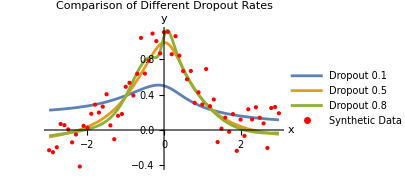

```mathematica
targetFunction[x_]:=Exp[-x^2];
syntheticData=Table[
x->targetFunction[x]+RandomVariate[NormalDistribution[0,0.15]],
{x,-3,3,0.1}
];

dropoutRates={0.1,0.5,0.8};

neuralNetworks=Table[
NetChain[
{
100,Tanh,DropoutLayer[rate],
100,Tanh,
1
}
],
{rate,dropoutRates}
];

trainingNetworks=Table[
NetTrain[
network,
syntheticData,
LearningRate->0.01,
MaxTrainingRounds->5000
],
{network,neuralNetworks}
];

Show[
Plot[
{trainedNetworks[[1]][x],trainedNetworks[[2]][x],trainedNetworks[[3]][x]},
{x,-3,3},
ImageSize->300,
PlotRange->All,
PlotLegends->{"Dropout 0.1","Dropout 0.5","Dropout 0.8"},
PlotLabel->"Comparison of Different Dropout Rates",
AxesLabel->{"x","y"}
],
ListPlot[
List@@@syntheticData,
PlotStyle->{Red,PointSize[0.01]},
PlotLegends->{"Synthetic Data"}
]
]
```

code 8.12

(* The code demonstrates the effect of different dropout rates with L2 regularization on the performance of neural networks trained on synthetic data generated from the function f(x)=exp(−x^2) with added Gaussian noise. With L2 regularization, the weights of the neural network are constrained, which often leads to smoother and more stable predictions. In the figures, the predicted curves for networks trained with L2 regularization will appear smoother, better match the general trend of the data, showing less sensitivity to the noise, and less jagged compared to those without L2 regularization: *)

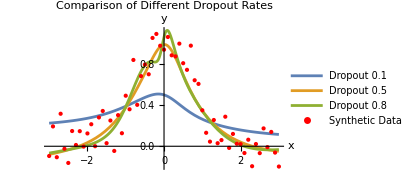

```mathematica
targetFunction[x_]:=Exp[-x^2];
syntheticData=Table[
x->targetFunction[x]+RandomVariate[NormalDistribution[0,0.15]],
{x,-3,3,0.1}
];

dropoutRates={0.1,0.5,0.8};

neuralNetworks=Table[
NetChain[
{
100,Tanh,DropoutLayer[rate],
100,Tanh,
1
}
],
{rate,dropoutRates}
];

trainingNetworks=Table[
NetTrain[
network,
syntheticData,
LearningRate->0.01,
MaxTrainingRounds->5000,
Method->{"SGD","L2Regularization"->0.01}
],
{network,neuralNetworks}
];

Show[
Plot[
{trainedNetworks[[1]][x],trainedNetworks[[2]][x],trainedNetworks[[3]][x]},
{x,-3,3},
ImageSize->300,
PlotRange->All,
PlotLegends->{"Dropout 0.1","Dropout 0.5","Dropout 0.8"},
PlotLabel->"Comparison of Different Dropout Rates",
AxesLabel->{"x","y"}
],
ListPlot[
List@@@syntheticData,
PlotStyle->{Red,PointSize[0.01]},
PlotLegends->{"Synthetic Data"}
]
]
```